```mathematica
Quit[];
```

# Extrapolate pk

Alejandro Aviles
avilescervantes@gmail.com

```mathematica
SetDirectory[NotebookDirectory[]];

inputfilepkl="CkappaT.dat";
outputfilepkl="CkappaT_ep.dat";
```

## import pk

1.

100000.

time = 0.00161 seconds

InterpolatingFunction[{{0.000943604, 216838.}}, <>]

0.000943604

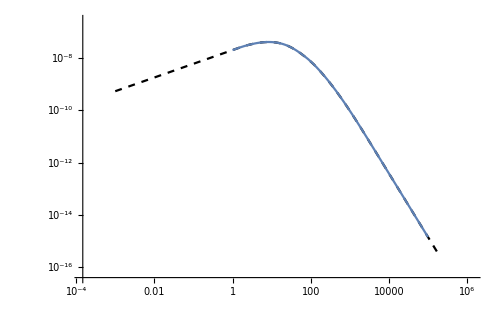

```mathematica
inputpkT=Import[inputfilepkl,"Table"];
kinMin=inputpkT[[1,1]]
kinMax=inputpkT[[-1,1]]
kcutmin=Max[1,kinMin];
kcutmax=Min[10000,kinMax];

(*kcutmin=0.001;
kcutmax=2;*)


(*exagerando:*)
kmin=10^(-3); 
kmax=200000;


<<extrapolate.m
ta=AbsoluteTime[];
PSLT=ExtrapolatekLogLog[inputpkT,kcutmin,kmin,kcutmax,kmax];
Print["time = ",AbsoluteTime[]-ta," seconds"];
PSL=Interpolation[PSLT]

kInputMin=PSLT[[1,1]]
kInputMax=PSLT[[-1,1]];

LogLogPlot[PSL[k],{k,kinMin,kinMax}];


inputpk=Interpolation[inputpkT];
LogLogPlot[{inputpk[k]},{k,kinMin,kinMax}];
LogLogPlot[{PSL[k]},{k,kmin,kmax},PlotStyle->{Black,Dashed},ImageSize->500];
Show[%,%%]
```

```mathematica
Nkout=1000.;
d=Log[kmax/kmin]/(Nkout-1);
kTout=Table[kmin Exp[d*(i-1)],{i,1,Nkout}];
pkout=Table[{kTout[[i]],PSL[kTout[[i]]]},{i,1,Nkout}];
```

```mathematica
Export[outputfilepkl,pkout,"Table"]
```

CkappaT_ep.dat